# Computação Natural - Aula 4 - Inteligência de Enxame

## Colônias de Formiga

### Ant Colony Optimization (ACO)

```mathematica
AntTour[vlist_,startingvertex_,pmatrix_,dmatrix_,alpha_,beta_]:=Module[{tour=Join[{},{RandomChoice[Complement[vlist,{startingvertex}]]}],remaining,eweights=(pmatrix^alpha)*((N[1/dmatrix])^beta)},
remaining=Complement[vlist,tour];
While[remaining!={},
tour=Join[tour,{With[{p=pmatrix⟦Last[tour],remaining⟧},RandomChoice[p/Total[p]->remaining]]}];
remaining=Complement[vlist,tour]
];
tour=Partition[Join[tour,{First[tour]}],2,1];
{tour,dmatrix⟦First[#],Last[#]⟧&/@tour}
];
```

```mathematica
ColonyStep[nAnts_,vlist_,startingvertex_,pmatrix_,dmatrix_,alpha_,beta_,Q_]:=
Module[{tours=Table[AntTour[vlist,startingvertex,pmatrix,dmatrix,alpha,beta],{nAnts}],besttour,mindist,p,deltapmatrix=Table[0,{Length[pmatrix]},{Length[pmatrix]}]},
p=First[Flatten[Position[Total[#⟦2⟧&/@tours],Min[Total[#⟦2⟧&/@tours]]]]];
besttour=tours⟦p,1⟧;
mindist=Total[tours⟦p,2⟧];
Table[If[MemberQ[besttour,tours⟦t,1,j⟧],deltapmatrix⟦tours⟦t,1,j,1⟧,tours⟦t,1,j,2⟧⟧+=Q/mindist],{t,1,nAnts},{j,1,Length[vlist]}];
{besttour,deltapmatrix,mindist}
];
```

```mathematica
ColonyRun[nAnts_Integer,vlist_,startingvertex_,p0_,dmatrix_,alpha_,beta_,Q_,decay_,itmax_Integer]:=
Module[{pmatrix=Table[p0,{i,1,Length[vlist]},{j,1,Length[vlist]}],besttour={},mindist=Infinity,i=1},
While[i<=itmax,
With[{next=ColonyStep[nAnts,vlist,startingvertex,pmatrix,dmatrix,alpha,beta,Q]},
If[next⟦3⟧<mindist,mindist=next⟦3⟧;besttour=next⟦1⟧];
pmatrix*=(1-decay);
pmatrix+=next⟦2⟧;
];
i++
];
{besttour,pmatrix,Total[dmatrix⟦#⟦1⟧,#⟦2⟧⟧&/@besttour]}
];
```

```mathematica
ShowPaths[tour_,pmatrix_]:=Module[{N=Length[pmatrix],min=Min[Flatten[pmatrix]]},
Graph[Range[1,Length[pmatrix]],Flatten[Table[Rule[i,j],{i,1,Length[pmatrix]},{j,1,Length[pmatrix]}],1],GraphHighlight->(Rule[#⟦1⟧,#⟦2⟧]&/@tour)]
];
```

```mathematica
ShowPaths[tour_,pmatrix_,vpositions_]:=Module[{N=Length[pmatrix],min=Min[Flatten[pmatrix]]},
Graph[Range[1,Length[pmatrix]],Rule[#⟦1⟧,#⟦2⟧]&/@tour,VertexCoordinates->vpositions]
];
```

## Exemplo 1: ACO para Problema do Caixeiro Viajante

```mathematica
Ex1nCities=10;
Ex1cRange=10;
Ex1Cities=Module[{c=Union[Table[{RandomReal[{0,Ex1cRange}],RandomReal[{0,Ex1cRange}]},Ex1nCities]]},
While[Length[c]<Ex1nCities,
c=Union[Table[{RandomInteger[{0,Ex1cRange}],RandomInteger[{0,Ex1cRange}]},Ex1nCities]]
];
c
]
```

{{1.07433,5.93647},{1.54379,2.19311},{2.2881,2.46202},{2.39668,3.68021},{4.50277,8.08859},{5.50913,0.961341},{6.18261,7.93994},{6.9268,5.52208},{7.97583,8.21353},{9.15115,0.459356}}

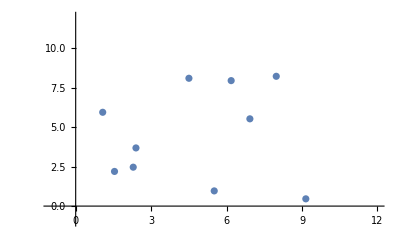

```mathematica
ListPlot[Ex1Cities,PlotRange->{{-1,12},{-1,12}}]
```

```mathematica
Ex1dmatrix=Table[If[i==j,Infinity,N[EuclideanDistance[Ex1Cities⟦i⟧,Ex1Cities⟦j⟧]]],{i,1,Ex1cRange},{j,1,Ex1cRange}];
Ex1dmatrix//MatrixForm
```

(∞ | 3.77268 | 3.68036 | 2.61521 | 4.04794 | 6.66478 | 5.48712 | 5.86712 | 7.26744 | 9.75878
3.77268 | ∞ | 0.791389 | 1.71431 | 6.59638 | 4.15225 | 7.38544 | 6.3292 | 8.81002 | 7.80242
3.68036 | 0.791389 | ∞ | 1.22302 | 6.04675 | 3.55346 | 6.72123 | 5.55711 | 8.08889 | 7.14927
2.61521 | 1.71431 | 1.22302 | ∞ | 4.88564 | 4.13275 | 5.69901 | 4.89024 | 7.18873 | 7.4831
4.04794 | 6.59638 | 6.04675 | 4.88564 | ∞ | 7.19795 | 1.68641 | 3.53029 | 3.4753 | 8.93379
6.66478 | 4.15225 | 3.55346 | 4.13275 | 7.19795 | ∞ | 7.01103 | 4.77599 | 7.66021 | 3.67645
5.48712 | 7.38544 | 6.72123 | 5.69901 | 1.68641 | 7.01103 | ∞ | 2.5298 | 1.81396 | 8.04807
5.86712 | 6.3292 | 5.55711 | 4.89024 | 3.53029 | 4.77599 | 2.5298 | ∞ | 2.88866 | 5.52982
7.26744 | 8.81002 | 8.08889 | 7.18873 | 3.4753 | 7.66021 | 1.81396 | 2.88866 | ∞ | 7.84274
9.75878 | 7.80242 | 7.14927 | 7.4831 | 8.93379 | 3.67645 | 8.04807 | 5.52982 | 7.84274 | ∞)

```mathematica
ColonyRun[nAnts_Integer,vlist_,startingvertex_,p0_,dmatrix_,alpha_,beta_,Q_,decay_,itmax_Integer]
```

```mathematica
Ex1Solution=ColonyRun[100,Range[1,Ex1nCities],1,1,Ex1dmatrix,2,1,1,0,100]
```

{{{5,1},{1,2},{2,3},{3,4},{4,6},{6,10},{10,8},{8,9},{9,7},{7,5}},{{1,12.085,1.89948,2.77161,4.024,3.10741,5.50989,1.26953,3.48582,2.06343},{3.391,1,7.26366,1.84322,7.12052,4.65422,1.91362,1.51661,3.07817,4.75258},{3.92696,1.89248,1,11.048,2.71081,1.46825,5.85697,5.41926,2.35218,1.81973},{2.91153,3.9139,12.3941,1,5.31057,3.79804,2.03873,2.25483,1.22424,3.76043},{3.52451,4.52283,2.21508,4.07454,1,2.09302,1.78388,1.73244,20.0534,2.19848},{1.75519,1.75784,3.87982,4.2716,2.4204,1,2.04541,2.51651,2.30819,22.4365},{4.7378,2.43485,2.62232,2.59885,1.77818,3.41037,1,16.835,4.00667,1.8123},{1.7089,4.82457,1.81038,3.97734,9.76869,2.62298,2.78038,1,4.55006,3.06007},{2.27602,1.88516,2.52582,2.65938,1.95689,12.3489,9.46273,3.89223,1,1.96263},{12.4814,3.79617,2.80112,2.84134,1.55062,3.89207,4.15391,4.90937,1.50039,1}},29.5631}

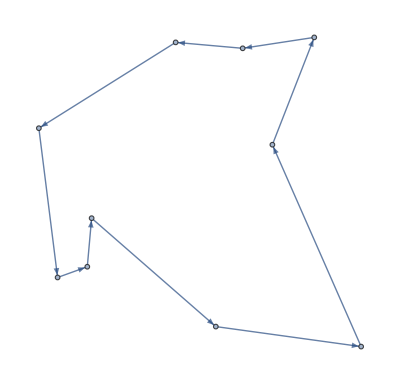

```mathematica
ShowPaths[Ex1Solution⟦1⟧,Ex1Solution⟦2⟧,Ex1Cities]
```

## Enxame de Partículas

### Particle Swarm Optimization (PSO)

```mathematica
PSO[f_,nParticles_Integer,pRanges_List,w_,cognitivecoeff_,socialcoeff_,maxit_Integer]:=
Module[{particles=Transpose@Table[RandomReal[{i⟦1⟧,i⟦2⟧}],{i,pRanges},{j,1,nParticles}],velocities=Table[RandomReal[{0,0.1}],nParticles],it=1,gbest=-Infinity,gbestpos,pbest=Table[-Infinity,nParticles],pbestpos=Table[{},nParticles],eval},
While[it<=maxit,
eval=Apply[f,#]&/@particles;
Table[If[eval⟦i⟧>pbest⟦i⟧,pbest⟦i⟧=eval⟦i⟧;pbestpos⟦i⟧=particles⟦i⟧],{i,nParticles}];
If[Max[eval]>gbest,gbest=Max[eval];gbestpos=particles⟦First[Flatten[Position[eval,Max[eval]]]]⟧];
Table[velocities⟦i⟧=w*velocities⟦i⟧+RandomReal[]*cognitivecoeff*(pbest⟦i⟧-particles⟦i⟧)+RandomReal[]*socialcoeff*(gbestpos-particles⟦i⟧),{i,1,nParticles}];
Table[particles⟦i⟧=particles⟦i⟧+velocities⟦i⟧,{i,1,nParticles}];
Table[Table[If[particles⟦i,j⟧>pRanges⟦j,2⟧,particles⟦i,j⟧=pRanges⟦j,2⟧],{j,1,Length[pRanges]}],{i,1,nParticles}];
Table[Table[If[particles⟦i,j⟧<pRanges⟦j,1⟧,particles⟦i,j⟧=pRanges⟦j,1⟧],{j,1,Length[pRanges]}],{i,1,nParticles}];
it++;
];
{gbestpos,gbest}
];
```

### Exemplo 2: Maximização de uma Função

```mathematica
Ex2AF[x_,y_]:=x^2+y^2-4;
Plot3D[Ex2AF[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
PSO[Ex2AF,1000,{{0,1},{0,1}},0.4,0.5,0.5,100]
```

```mathematica
Ex2BF[x_,y_]:=-x^2-y^2+4;
Plot3D[Ex2BF[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
PSO[Ex2BF,1000,{{0,1},{0,1}},0.4,0.5,0.5,100]
```

```mathematica
Ex2CF[x_,y_]:=Sin[x^2+x*y+y^2];
Plot3D[Ex2CF[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
PSO[Ex2CF,1000,{{0,1},{0,1}},0.4,0.5,0.5,100]
```

```mathematica
Ex2DF[x_,y_]:=x*y*Sin[x^2+y^2];
Plot3D[Ex2DF[x,y],{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
PSO[Ex2DF,1000,{{0,1},{0,1}},0.4,0.5,0.5,100]
```

### Exemplo 3: Ajuste de parâmetros por meio de um PSO

#### Funções referentes a AGs

```mathematica
RouletteSelection[pool_,fitness_,n_]:=With[{p=fitness/Total[fitness]},RandomChoice[p-> pool,n]];
```

```mathematica
AG[pop_List,fFun_,cFun_,mFun_,pm_,maxit_Integer,fGoal_:Infinity,sType_:All,showHistory_:False]:=
Module[{population=pop,popfitness=fFun[#]&/@pop,offspring={},offfitness,L=Length[pop],history={},i=1},
history=Join[history,{{MapThread[List,{population,popfitness}],Max[popfitness],Mean[popfitness]}}];
While[i≤maxit&&Max[popfitness]<fGoal,
offspring=mFun[cFun[population],pm];
offfitness=fFun[#]&/@offspring;
If[sType==All,
population=RouletteSelection[Join[population,offspring],Join[popfitness,offfitness],L],
population=RouletteSelection[offspring,offfitness,L]
];
popfitness=fFun[#]&/@population;
history=Join[history,{{MapThread[List,{population,popfitness}],Max[popfitness],Mean[popfitness]}}];
i++;
];
With[{M=Max[popfitness]},
If[!showHistory,
{MapThread[List,{population,popfitness}],M,Mean[popfitness]},
history
]
]
];
```

```mathematica
FitnessReport[historico_]:=Transpose[{#⟦2⟧,#⟦3⟧}&/@historico];
```

```mathematica
BestReport[historico_]:=Table[g⟦1⟧⟦First[Flatten[Position[g⟦2⟧,Max[g⟦2⟧]]]]⟧,{g,Transpose[#⟦1⟧]&/@historico}];
```

#### PCV da Aula 2 (codificação inicial)

```mathematica
cidades={{9,9},{3,10},{4,7},{7,7},{1,1},{1,10},{2,9},{2,3},{1,6},{6,9}};
```

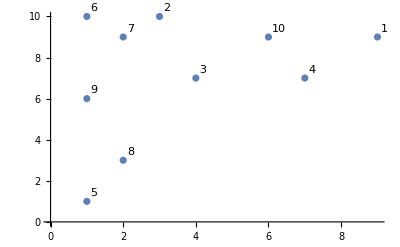

```mathematica
ListPlot[Labeled[#⟦1⟧,#⟦2⟧]&/@MapThread[List,{cidades,Range[1,10]}]]
```

```mathematica
matrizdistancias=Table[N[EuclideanDistance[cidades⟦i⟧,cidades⟦j⟧],4],{i,1,10},{j,1,10}];
MatrixForm[matrizdistancias]
```

(0 | 6.083 | 5.385 | 2.828 | 11.31 | 8.062 | 7. | 9.22 | 8.544 | 3.
6.083 | 0 | 3.162 | 5. | 9.22 | 2. | 1.414 | 7.071 | 4.472 | 3.162
5.385 | 3.162 | 0 | 3. | 6.708 | 4.243 | 2.828 | 4.472 | 3.162 | 2.828
2.828 | 5. | 3. | 0 | 8.485 | 6.708 | 5.385 | 6.403 | 6.083 | 2.236
11.31 | 9.22 | 6.708 | 8.485 | 0 | 9. | 8.062 | 2.236 | 5. | 9.434
8.062 | 2. | 4.243 | 6.708 | 9. | 0 | 1.414 | 7.071 | 4. | 5.099
7. | 1.414 | 2.828 | 5.385 | 8.062 | 1.414 | 0 | 6. | 3.162 | 4.
9.22 | 7.071 | 4.472 | 6.403 | 2.236 | 7.071 | 6. | 0 | 3.162 | 7.211
8.544 | 4.472 | 3.162 | 6.083 | 5. | 4. | 3.162 | 3.162 | 0 | 5.831
3. | 3.162 | 2.828 | 2.236 | 9.434 | 5.099 | 4. | 7.211 | 5.831 | 0)

```mathematica
Ex3DrawRoute[rota_,fitness_]:=Labeled[Graph[Range[1,10],Join[Table[rota⟦i⟧->rota⟦i+1⟧,{i,1,9}],{rota⟦10⟧->rota⟦1⟧}],VertexCoordinates->cidades,VertexLabels->"Name"],1/fitness];
```

```mathematica
ComprimentoRota[rota_]:=Total[Table[matrizdistancias⟦rota⟦i⟧,rota⟦i+1⟧⟧,{i,1,9}]]+matrizdistancias⟦rota⟦10⟧,rota⟦1⟧⟧;
```

```mathematica
Ex3Fitness[x_]:=1/ComprimentoRota[x];
```

```mathematica
OrderedReplace[p1_List,p2_List,range_List]:=ReplacePart[p2/.MapThread[Rule,{Complement[Range[1,10],p2⟦#⟧&/@range],Complement[Range[1,10],p1⟦#⟧&/@range]}],MapThread[Rule,{range,p1⟦#⟧&/@range}]];
```

```mathematica
Ex3Crossover[x_,y_]:=With[{range=Range[Min[#],Max[#]]&@{RandomInteger[{1,10}],RandomInteger[{1,10}]}},{OrderedReplace[x,y,range],OrderedReplace[y,x,range]}];
Ex3Crossover[pop_]:=Flatten[Ex3Crossover[#⟦1⟧,#⟦2⟧]&/@Partition[pop,2],1];
```

```mathematica
Ex3Mutation[pop_,pm_]:=Table[If[RandomReal[]≤pm,With[{parts=RandomSample[Range[1,10],2]},ReplacePart[x,{parts⟦1⟧->x⟦parts⟦2⟧⟧,parts⟦2⟧->x⟦parts⟦1⟧⟧}]],x],{x,pop}];
```

#### Busca no espaço de taxas de mutação

```mathematica
Ex3PopSize=100;
Ex3PopInicial=Table[RandomSample[Range[1,10],10],{Ex3PopSize}];
```

```mathematica
Ex3pm=0.2;
Ex3maxit=100;
```

```mathematica
AG[Ex3PopInicial,Ex3Fitness,Ex3Crossover,Ex3Mutation,Ex3pm,Ex3maxit,Infinity,All,False]⟦2⟧
```

0.03234

```mathematica
Ex3PSOf[x_]:=-(AG[Ex3PopInicial,Ex3Fitness,Ex3Crossover,Ex3Mutation,x,Ex3maxit,Infinity,All,False]⟦2⟧);
```

```mathematica
Ex3PSORun=PSO[Ex3PSOf,10,{{0.0,0.3}},0.5,0.5,0.5,10]
```

{{0.103384},-0.02409}

```mathematica
Ex3Routes=With[{ag=AG[Ex3PopInicial,Ex3Fitness,Ex3Crossover,Ex3Mutation,Ex3PSORun,Ex3maxit,Infinity,All,False]},Select[ag⟦1⟧,(#⟦2⟧==ag⟦2⟧)&]]
```

```mathematica
Ex3DrawRoute[Ex3Routes⟦1,1⟧,Ex3Routes⟦1,2⟧]
```